```mathematica
ClearAll[MaxMinorNorm,TestSequenceGrowth];

(*Function to compute the maximum minor M_1k for given d,m,and sequence a_k*)
MaxMinorNorm[aSeq_,d_,m_]:=Module[{Ddeg,aCoefs,poly,convCoefs,A,Aprime,k,i,j,row,col,minors},Ddeg=(d+1) (m+1);
(*Generate sequence up to Ddeg-2*)(*Note:If the series starts at k=1,aSeq[0] should evaluate to 0*)aCoefs=Table[aSeq[n],{n,0,Ddeg-2}];
poly=Sum[aCoefs[[n+1]] x^n,{n,0,Ddeg-2}];
(*Compute j-fold convolutions of a_k using polynomial expansion*)convCoefs=Table[PadRight[CoefficientList[Series[poly^idx,{x,0,Ddeg-2}],x],Ddeg-1],{idx,0,d}];
(*Construct matrix A based on Equation (11) and (13)*)A=Table[i=Quotient[col,m+1];
j=Mod[col,m+1];
If[row>=j,convCoefs[[i+1,row-j+1]],0],{row,0,Ddeg-2},{col,0,Ddeg-1}];
(*A' is A with the first column removed (p_0^(0) removed)*)Aprime=A[[All,2;;]];
(*Calculate minors M_1k by removing 1st row and k-th column of Aprime*)minors=Table[Abs[Det[Drop[Aprime,{1},{k}]]],{k,1,Ddeg-1}];
Max[minors]]

(*Driver function to test the asymptotic growth rate (gamma) over a range of m*)
TestSequenceGrowth[aSeq_,d_,mMax_]:=Module[{results,maxM,gammaEst},Print["Testing growth for d = ",d];
Print["m \t\t  γ^d \t\t γ"];
Print["----------------------------------------------------------"];
results=Table[maxM=MaxMinorNorm[aSeq,d,m];
(*Estimate gamma^d by taking the m-th root of the maximal minor*)gammaEst=If[maxM>0,N[maxM^(1/m)],0];
Print[m," \t\t ",gammaEst," \t\t ",gammaEst^(1/d)];
{m,maxM,gammaEst},{m,1,mMax}];
(*Plot the log of the maximum minor to visualize linearity (exponential growth)*)ListLogPlot[results[[All,{1,2}]],PlotLabel->"Growth of \!\(\*SubscriptBox[\(M\), \(1, k\)]\)",AxesLabel->{"m","Log(\!\(\*SubscriptBox[\(M\), \(1, k\)]\))"},Joined->True,Mesh->All]]
```

Testing growth for d = 2

m 		  γ^d 		 γ

----------------------------------------------------------

1 		 1. 		 1.

2 		 2. 		 1.41421

3 		 3.70843 		 1.92573

4 		 3.7885 		 1.94641

5 		 3.4822 		 1.86607

6 		 4.60578 		 2.14611

7 		 4.67149 		 2.16136

8 		 5.07653 		 2.25312

9 		 4.44324 		 2.1079

10 		 4.91215 		 2.21634

11 		 4.96332 		 2.22785

12 		 5.59655 		 2.3657

13 		 6.43851 		 2.53742

14 		 6.12201 		 2.47427

15 		 6.24479 		 2.49896

16 		 5.88288 		 2.42547

17 		 6.93327 		 2.63311

18 		 7.30897 		 2.70351

19 		 6.66498 		 2.58166

20 		 7.25197 		 2.69295

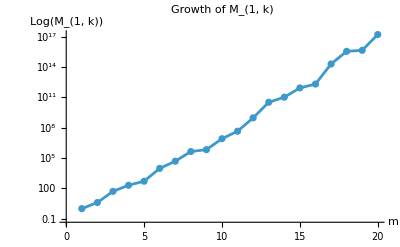

```mathematica
(*Define a_k=mu(k)^2,starting at k=1. Set a_0=0*)aMoebiusSq[0]=0;
aSq[k_]:=MoebiusMu[k]^2;

(*Test for d=2,up to m=15*)
TestSequenceGrowth[aSq,2,20]
```